```mathematica
r=2 .529*10^-10;
Plot3D[(1/r^2)*(1-(Cot[ϕ]^2/Sin[θ]^2*(0.729-1-r/(2*.529*10^-10))^2)),{ϕ,0,Pi},{θ,0,Pi},ColorFunction->"BlueGreenYellow",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
θ=Pi/2;
Plot3D[(1/r^2)*(1-(Cot[ϕ]^2/Sin[θ]^2*(0.729-1-r/(2*.529*10^-10))^2)),{ϕ,0,Pi},{r,.529*10^-10,20*.529*10^-10},ColorFunction->"BlueGreenYellow",AxesLabel->Automatic]
```

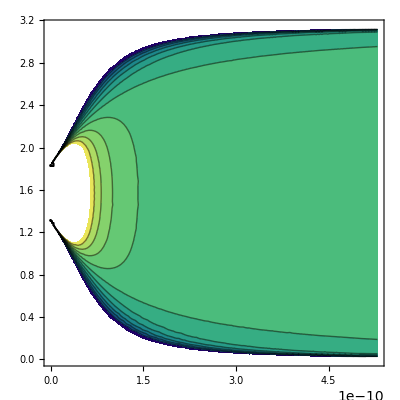

```mathematica
ContourPlot[(1/r^2)*(1-(Cot[theta]^2/(.729-1-r/(2*.529*10^-10))^2)),{r,0,2*5*.529*10^-10},{theta,0,Pi},ColorFunction->"BlueGreenYellow"]
```

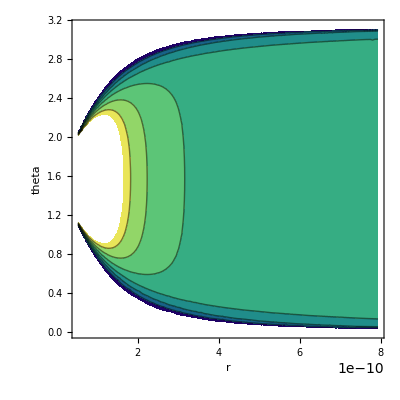

```mathematica
ContourPlot[(1/r^2)*(1-(Cot[theta]^2/(0.999-1-r/(2*.529*10^-10))^2)),{r,.529*10^-10,15*.529*10^-10},{theta,0,Pi},ColorFunction->"BlueGreenYellow",AxesLabel->Automatic]
```

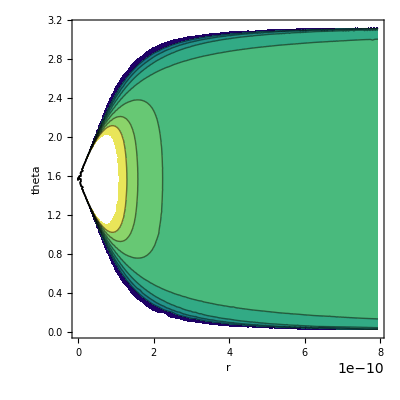

```mathematica
ContourPlot[(1/r^2)*(1-(Cot[theta]^2/(0.999-1-r/(2*.529*10^-10))^2)),{r,0,15*.529*10^-10},{theta,0,Pi},ColorFunction->"BlueGreenYellow",AxesLabel->Automatic]
```

```mathematica
Plot3D[(1/x^2)*(1-(Cot[y]^2/(.9999733-1-x/(2*.529*10^-10))^2)),{x,2*.529*10^-10,4*.529*10^-10},{y,0,Pi},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

```mathematica
ClearAll;
γ=0.72999;
a=0.529*10^-10;
r=2 a; (*Fixing r*)
Plot3D[1/r^2(1-Cot[ϕ]^2/(Sin[θ]^2(γ-1-r/(2*a))^2)) ,{ϕ,0,Pi},{θ,0,Pi},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Plot of S(t) the scale factor*)
scalefactor2:= r^(2γ-4) a^(4-2γ)ⅇ^(-r/a)Cos[θ]^2 Sin[ϕ]^2 Cos[2*w*t];
ClearAll;
γ=0.99999;
a=a;
r=2 a; (*Fixing r*)
T=1;
Plot3D[Sqrt[r^(2γ-4) a^(4-2γ)ⅇ^(-r/a)Cos[θ]^2 Cos[(2Pi)/T*t]],{t,0,T/4},{θ,Pi/2,3Pi/2},AxesLabel->Automatic,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
(*Plot of S(t) the scale factor*)
scalefactor2:= r^(2γ-4) a^(4-2γ)ⅇ^(-r/a)Cos[θ]^2 Sin[ϕ]^2 Cos[2*w*t];
ClearAll;
γ=0.99999;
a=a;
r=2 a; (*Fixing r*)
T=1;
Plot3D[Sqrt[r^(2γ-4) a^(4-2γ)ⅇ^(-r/a)Cos[θ]^2 Cos[(2Pi)/T*t]],{t,T/2,3T/2},{θ,Pi/2,3Pi/2},AxesLabel->Automatic,ColorFunction->"Rainbow"]
```

-Graphics3D-